```mathematica
r23 := (r3 - a3  Exp[I ϕ3])/(1-r2 a3 Exp[I ϕ3])
r12 := (r2 - a2 r23  Exp[I ϕ2])/(1-r2 r23 a2  Exp[I ϕ2])
transtriple:=(r1 - r12 a1  Exp[I ϕ1])/(1-r1  r12  a1  Exp[I ϕ1])
```

```mathematica
n:=3.45;
R1:=10 10^(-6);
R2:=10 10^(-6);
d1:= 2 Pi R1
d2:= 2 Pi R2
λ:=1550 10^(-9); (* resonant wavelength *)
Q1:=1×10^5;
Q2:=1×10^6;
Q3:=1×10^7;
g1 := 130.00
g2 := 12.00
g3 := 1.01
α1:=(2 Pi n)/(λ  Q1) (*139.85*)
α2:=(2 Pi n)/(λ  Q2)(*13.98*)
α3:=(2 Pi n)/(λ  Q3)(*1.39*)
a1:= Exp[-(α1-g1) d1]
a2:= Exp[-(α2-g2) d2]
a3:= Exp[-(α2-g2) d2]
t1:=√(1-r1^2)
t2:=√(1-r2^2)
t3:=√(1-r3^2)
r1:= 0.9889
r2:= 0.9989
r3:= 0.9998
```

```mathematica
ϕ2 := ϕ1 
ϕ3 := ϕ1
```

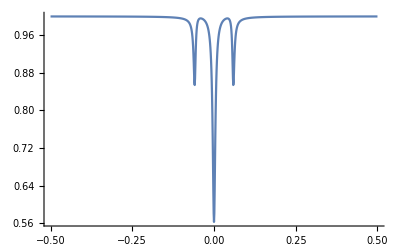

```mathematica
ϕ1min:=-0.5;
ϕ1max:=0.5;
transtripledata:=Table[{ϕ1,Abs[transtriple]^2},{ϕ1,ϕ1min, ϕ1max, 0.001}]
ListLinePlot[transtripledata,PlotRange->All]
```

```mathematica
ϕ23 := Pi + ϕ1 + 2 ArcTan[(r3 Sin[ϕ1])/(1-r3 Cos[ϕ1])]
ϕ12 := ArcTan[(a2 Abs[r23] Sin[ϕ1 + ϕ23])/(r2-a2 Abs[r23] Cos[ϕ1 + ϕ23])] - ArcTan[(r2 a2 Abs[r23] Sin[ϕ1 + ϕ23])/(1- r2 a2 Abs[r23] Cos[ϕ1 + ϕ23])]
ϕeff := ArcTan[(a1 Abs[r12] Sin[ϕ1 + ϕ12])/(r1-a1 Abs[r12] Cos[ϕ1 + ϕ12])] - ArcTan[(r1 a1 Abs[r12] Sin[ϕ1 + ϕ12])/(1- r1 a1 Abs[r12] Cos[ϕ1 + ϕ12])]
```

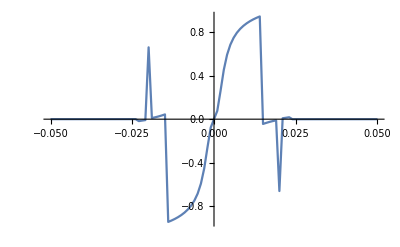

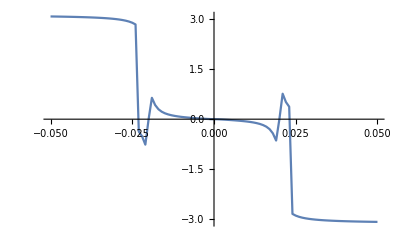

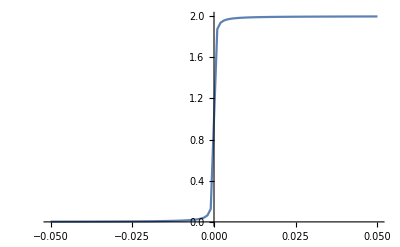

```mathematica
ϕ1min:=-0.05;
ϕ1max:=0.05;
transdata:=Table[{ϕ1,ϕeff/Pi},{ϕ1,ϕ1min, ϕ1max, 0.001}]
ListLinePlot[transdata,PlotRange->All]
transdata:=Table[{ϕ1,ϕ12},{ϕ1,ϕ1min, ϕ1max, 0.001}]
ListLinePlot[transdata,PlotRange->All]
transdata:=Table[{ϕ1,ϕ23/ Pi},{ϕ1,ϕ1min, ϕ1max, 0.001}]
ListLinePlot[transdata,PlotRange->All]
```